```mathematica
phiBar[deltaPhi_,T_]:=deltaPhi/T;
```

```mathematica
Cp6:=phiBar/(√π(1-3/(2 κ))^(3/2))Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

```mathematica
IE1=Cp6 * Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ - 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->κ>3/2&&phiBar>0]
```

-(-(12+8 phiBar-8 κ)^-κ √((6+4 phiBar-4 κ)/phiBar) (-3+2 κ)^(1+κ) Gamma[1-κ] Gamma[-1+2 κ]+(3 Gamma[κ]-2 Gamma[1+κ]) Hypergeometric2F1[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/(2 √π (1-3/(2 κ))^(3/2) κ^(3/2) Gamma[-1/2+κ])

```mathematica
IE2=Cp6 * 1/(RB-1)Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarOverRBm1>0]
```

(phiBar Gamma[1+κ] ((-(3-2 κ)^2+8 phiBarOverRBm1^2 κ+2 phiBarOverRBm1 (3-8 κ+4 κ^2)) Hypergeometric2F1[1,1+κ,-1/2,(2 phiBarOverRBm1)/(3-2 κ)]+((3-2 κ)^2-4 phiBarOverRBm1^2 (-1+6 κ+4 κ^2)+phiBarOverRBm1 (-30+8 κ+8 κ^2)) Hypergeometric2F1[1,1+κ,1/2,(2 phiBarOverRBm1)/(3-2 κ)]))/(2 phiBarOverRBm1^2 √π (-1+RB) (1-3/(2 κ))^(3/2) κ^(3/2) (-1+4 κ^2) Gamma[-1/2+κ])

### Whoops, this version had the sign of IE2 reversed

```mathematica
FullThing=FullSimplify[IE1+IE2/.phiBarOverRBm1->phiBar/(RB-1)]
```

1/(16 (-3+2 κ)^(3/2))(1/(phiBar^2 (-1+RB) Gamma[5/2+κ])√(2/π) Gamma[1+κ] ((-1+RB) (-3+2 κ) (-(-1+RB)^2 (3-2 κ)^2-2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)+4 phiBar^2 (-1+6 κ+4 κ^2))+(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+8 Csc[π κ] ((3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(1+κ)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]))

```mathematica
(*densFacK[phiBar_,κ_,RB_]:=1/(16 (-3+2 κ)^(3/2))(1/(phiBar^2 (-1+RB) Gamma[5/2+κ])√(2/π) Gamma[1+κ] ((-1+RB) (-3+2 κ) (-(-1+RB)^2 (3-2 κ)^2-2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)+4 phiBar^2 (-1+6 κ+4 κ^2))+(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+8 Csc[π κ] ((3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(1+κ)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]))*)
```

### Here we go

```mathematica
FullThing=FullSimplify[IE1-IE2/.phiBarOverRBm1->phiBar/(RB-1)]
```

```mathematica
densFacK[phiBar_,κ_,RB_]:=
```

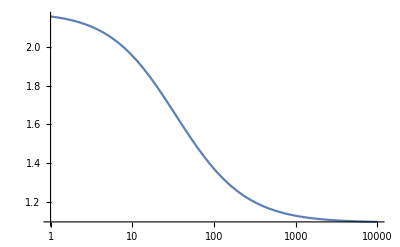

```mathematica
LogLinearPlot[densFacK[941/110,18/10,RB],{RB,1,10000}]
```

```mathematica
LogLinearPlot[densFacK[941/110,201/10,RB],{RB,1,10000}]
```

-Graphics-

```mathematica
Limit[densFacK[phiBar,κ,RB],κ->∞]
```

$Aborted